```mathematica
nbdir=NotebookDirectory[];
exptdir=StringDrop[nbdir,-StringLength["generating/"]]
```

/home/nicolas/git/reports/M2/oral/img/

```mathematica
(* Print default RGB color of Mathematica plots *)
blue=ColorData[1,1]
```

RGBColor[0.2472,0.24,0.6]

```mathematica
(* Rectangle of adjustable thickness and color *)
rect[coordslow_,coordsup_,color_,thickness_]:={FaceForm[{Black,Opacity[0]}],EdgeForm[{thickness,color}],Rectangle[coordslow,coordsup,RoundingRadius->.02]}
```

```mathematica
(* See! Just what I told ya. *)
Manipulate[Graphics[rect[{0,0},{1,1},RGBColor[r,g,b],Thickness[u]]],{u,0.01,0.2},{r,0,1},{g,0,1},{b,0,1}]
```

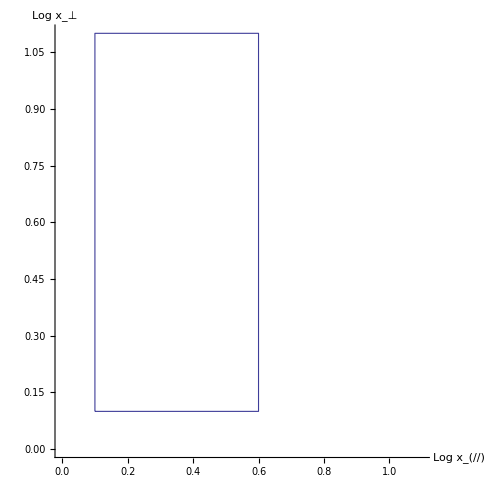

/home/nicolas/git/reports/M2/oral/img/blockspin_no_theta.pdf

```mathematica
delta=.1;
θ=1/2;
g1=Graphics[rect[{delta,delta},{delta+θ,delta+1},blue,Thick],Axes->True,Ticks->Automatic,PlotRange->{{0,1+delta},{0,delta+1}},AxesLabel->{"Log x_(//)","Log x_⊥"},AspectRatio->1]
Export[exptdir<>"blockspin_no_theta.pdf",%]
```

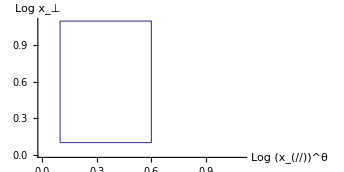

/home/nicolas/git/reports/M2/oral/img/blockspin_theta.pdf

```mathematica
g2=Graphics[rect[{delta,delta},{delta+θ,delta+1},blue,Thick],Axes->True,Ticks->Automatic,PlotRange->{{0,1+delta},{0,delta+1}},AxesLabel->{"Log (x_(//))^θ","Log x_⊥"},AspectRatio->1/2]
Export[exptdir<>"blockspin_theta.pdf",%]
```

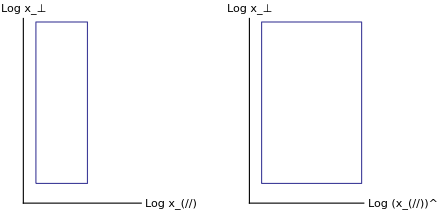

```mathematica
GraphicsRow[{g1,g2}]
```

```mathematica
-Graphics-
Export[exptdir<>"blockspin_theta.pdf",%]
```

-Graphics-

/home/nicolas/git/reports/M2/oral/img/blockspin_theta.pdf